```mathematica
P1 = Binomial[6, k]*r^(14k)*(1-r^14)^(6-k)
```

r^(14 k) (1-r^14)^(6-k) Binomial[6,k]

```mathematica
PH = Binomial[6, k]*(r^(14) + (1-r^14)/H)^k*(1-r^14)^(6-k)
```

```mathematica
P2 = Sum[P1, {k, 2, 6}]
```

r^84+6 r^70 (1-r^14)+15 r^56 (1-r^14)^2+20 r^42 (1-r^14)^3+15 r^28 (1-r^14)^4

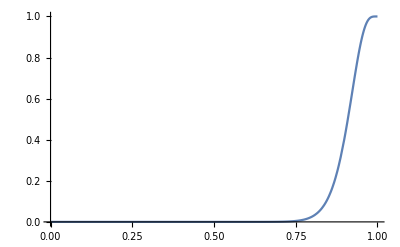

```mathematica
Plot[P2,{r,0,1}, PlotRange->{0, 1}]
```

```mathematica
r = .98
```

0.98

```mathematica
P2
```

0.995673

```mathematica
Clear[r]
```

```mathematica
P2
```

r^84+6 r^70 (1-r^14)+15 r^56 (1-r^14)^2+20 r^42 (1-r^14)^3+15 r^28 (1-r^14)^4